# HW 8 - ASTR501 Daniel George - dgeorge5@illinois.edu

```mathematica
Unprotect@Quantity;Quantity[0.|0,_]=0;Protect@Quantity;
SetOptions[Plot,{Filling->Bottom,ImageSize->250,AxesLabel->{"v (km/s)","T_B (K)"}}];
CO[nH_]:=2 nH LinguisticAssistant; ν0=Quantity[115.272, "Gigahertz"];
B0=Solve[Quantity[, "PlanckConstant"]ν0==Quantity[, "BoltzmannConstant"]B J(J+1)/2-0/.J->1,B][[1,1,2]];
g[j_]:=2j+1;f[T_,j_]:=g[j]Exp[- B0 /T j(j+1)/2]/Sum[g[i]Exp[- B0 i(i+1)/2/T],{i,0,8}];
ϕ=Exp[-(ν-(1+vz/Quantity[, "SpeedOfLight"])ν0)^2/(2 σ^2)]/(Sqrt[2π] σ);
n@i_:=f[T,i-1] CO[nH];    σν[v_]:=v/Quantity[, "SpeedOfLight"]ν0;   A21=LinguisticAssistant;
{B21,B12}=NSolve[{A21==2 Quantity[, "PlanckConstant"]ν0^3/Quantity[, "SpeedOfLight"]^2 b21,g@0 /g@1 ==b21/b12},{b12,b21}][[1,;;,2]];
jν[nH_,vz_,T_,σ_]=n@2 A21 Quantity[, "PlanckConstant"] ν/(4 π) ϕ;
αν[nH_,vz_,T_,σ_]=Quantity[, "PlanckConstant"]ν/(4π) (n@1 B12 -n@2 B21)ϕ;
TB[d_,nH_,vz_,Δv_,T_,nH2_:0,vz2_:1,Δv2_:1,T2_:1]:=ParametricNDSolveValue[UnitConvert@{Iν'@z /Quantity[1.0, "Parsecs"]==-(αν[nH,vz,T,σν@Δv]+αν[nH2,vz2,T2,σν@Δv2]) Iν@z+(jν[nH,vz,T,σν@Δv]+jν[nH2,vz2,T2,σν@Δv2]),Iν[-d]==2 Quantity[, "PlanckConstant"]ν^3/Quantity[, "SpeedOfLight"]^2/(Exp[Quantity[, "PlanckConstant"]ν/(Quantity[, "BoltzmannConstant"]Quantity[2.725, "Kelvins"])]-1)}/.Quantity[x_,_]:>x, QuantityMagnitude@UnitConvert[Quantity[, "SpeedOfLight"]^2/(2 Quantity[, "BoltzmannConstant"])/ν^2]Iν@0,{z,-d,0 },ν,MaxStepFraction->0.0001]@QuantityMagnitude[(1.+# Quantity[1., ("Kilometers")/("Seconds")]/Quantity[, "SpeedOfLight"])ν0,Quantity[1, "Hertz"]]&
```

#### a) and b)

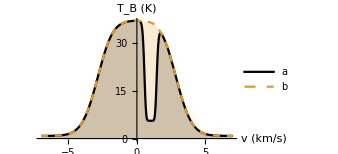

```mathematica
Plot[Evaluate@{TB[8,500 UnitBox[(z+5)/6],0,Quantity[1.5, ("Kilometers")/("Seconds")],Quantity[40, "Kelvins"],50 UnitBox[z+1],Quantity[1, ("Kilometers")/("Seconds")],Quantity[.2, ("Kilometers")/("Seconds")] ,Quantity[8, "Kelvins"]]@x,TB[8,500 UnitBox[(z+3)/6],0,Quantity[1.5, ("Kilometers")/("Seconds")],Quantity[40, "Kelvins"],50 UnitBox[z+7],Quantity[1, ("Kilometers")/("Seconds")],Quantity[.2, ("Kilometers")/("Seconds")] ,Quantity[8, "Kelvins"]]@x},{x,-7,7},PlotStyle->{Black,Dashed},PlotLegends->{"a","b"}]
```

Absorption occurs when the colder cloud is between the observer and the hot cloud.

#### c) and d)

```mathematica
σv=Solve[3 1/2 LinguisticAssistant vx^2==3/2 Quantity[, "BoltzmannConstant"]Quantity[10, "Kelvins"],vx][[2,1,2]]
```

54.483 m/s

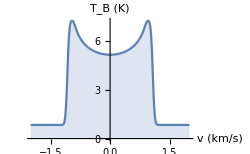

```mathematica
Plot[Evaluate@TB[1,50,Sin[2π z]Quantity[1., ("Kilometers")/("Seconds")],σv,Quantity[10, "Kelvins"]]@x,{x,-2,2}]
```

The peaks correspond to the extrema in the sine curve, where most of the velocities are concentrated.

#### e) No. There can also be dips due to absorption of cool gas or peculiar motion of low density gas.

#### f)

```mathematica
Quantity[, "SpeedOfLight"]^2/(2 Quantity[, "BoltzmannConstant"])/ν^2 2 Quantity[, "PlanckConstant"]ν^3/Quantity[, "SpeedOfLight"]^2/(Exp[Quantity[, "PlanckConstant"]ν/(Quantity[, "BoltzmannConstant"]Quantity[2.725, "Kelvins"])]-1)/.ν->Quantity[115, "Gigahertz"]//UnitConvert
```

0.838913 K

#### g)

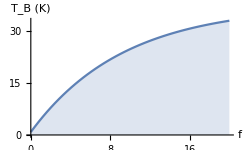

```mathematica
Plot[TB[1,x 50,0,Quantity[1, ("Kilometers")/("Seconds")],Quantity[40, "Kelvins"]]@0,{x,0,20},AxesLabel->{"f","T_B (K)"}]
```

Initially the profile is linear but then saturates below the thermal temperature due to high optical depth.

#### h)

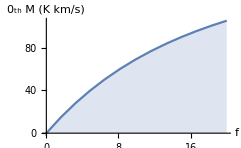

```mathematica
Plot[NIntegrate[Evaluate@(TB[1,x 50,0,Quantity[1, ("Kilometers")/("Seconds")],Quantity[40, "Kelvins"]]@v-TB[1, 50,0,Quantity[1, ("Kilometers")/("Seconds")],Quantity[40, "Kelvins"]]@5),{v,-5,5}],{x,0,20},AxesLabel->{"f","0_th M (K km/s)"},PlotPoints->4,MaxRecursion->2]
```

The curve of growth is initially linearly proportional to the column density of gas but then saturates due to high optical depth.